```mathematica
Clear["Global`*"]
Ca=10^-25;
e=1.602* 10^-19;
EC=e^2/(2*Ca);
kb=1.38* 10^-23;
Vg=0.03;
γL=1000000000;
γR=1000000000;
muD=5.5;
muL=5;
muR=6;
T=3;

fdist[En_,mu_,T_]:=1/(Exp[(En-mu)/(kb*T)]+1);
Nopt[Vg_]:=Floor[e*Vg/(2*EC)];
EN[n_]:=EC*n^2-e*Vg*n;
fE[En_]:=En/(Exp[En/(kb*T)]-1);
GamL[n1_,n2_,V_]:=γL*f[EN[n1]-EN[n2]+(n1-n2)*e*V/2];
GamR[n1_,n2_,V_]:=γR*f[EN[n1]-EN[n2]+(n1-n2)*e*V/2];
WE[n1_,n2_,V_]:=GamL[n1,n2,V]+GamR[n1,n2,V];
(*Define scattering probability matrix W*)
Wn[n_,V_]:=SparseArray[{Band[{1,2},{n-1,n},{1,1}]->Table[WE[i,i+1,V],{i,0,n-2}],Band[{1,1},{n,n},{1,1}]->Table[-WE[i+1,i,V]-WE[i-1,i,V],{i,0,n-1}],Band[{2,1},{n,n-1},{1,1}]->Table[WE[i,i-1,V],{i,0,n-2}]},{n,n}];
W[n_,V_]:={{WE[n,n-1,V],0,0},{0,-WE[n+1,n,V]-WE[n-1,n,V],0},{0,0,WE[n,n+1,V]}};
P[V_]:=Table[1,3].(Inverse[W[1,V]+IdentityMatrix[3]])

IL[V_]:=-e*Sum[(GamL[n+1,n,V]-GamL[n-1,n,V])*(P[V])[[2]],{n,1,20}]
```

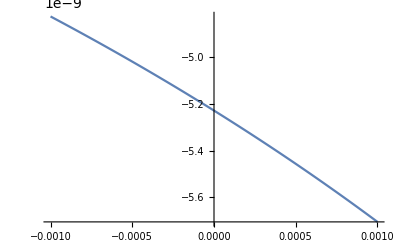

```mathematica
Plot[{N[P[V]][[2]]},{V,-0.001,0.001},PlotRange->All]
```

```mathematica
Clear["Global`*"]
Ca=10^-16;
e=1.602* 10^-19;
EC=e^2/(2*Ca);
kb=1.38* 10^-23;
gamma=1000000000;
g=2.002319;
muB=9.27400* 10^-24;
B=20;
deltaEb=B*muB*g;
alphag=1/20 ;
T=3;
muL=e*V/2;
muR=e*-V/2;
EN[n_]:=EC*n^2-e*Vg*n;
mu[n1_,n2_]:=EN[n1]-EN[n2]
Nopt[Vg_]:=Floor[e*Vg/(2*EC)]

f[mu1_,mu2_,T_]:=1/(Exp[(mu1-mu2)/(kb*T)]+1);

W10={f[mu[1,0],muL,T],f[mu[1,0],muR,T]};
W21={f[mu[2,1],muL,T],f[mu[2,1],muR,T]};
W32={f[mu[3,2],muL,T],f[mu[3,2],muR,T]};
W43={f[mu[4,3],muL,T],f[mu[4,3],muR,T]};
W01={1-f[mu[1,0],muL,T],1-f[mu[1,0],muR,T]};
W12={1-f[mu[2,1],muL,T],1-f[mu[2,1],muR,T]};
W23={1-f[mu[3,2],muL,T],1-f[mu[3,2],muR,T]};
W34={1-f[mu[4,3],muL,T],1-f[mu[4,3],muR,T]};
WMAT={{1,1,1,1},{Total[W10],-Total[W21]-Total[W01],Total[W12],0},{0,Total[W21],-Total[W12]-Total[W32],Total[W23]},{0,0,Total[W32],-Total[W23]}};
R={1,0,0,0};
P=LinearSolve[WMAT,R];
IL=-e*gamma*(-W01[[1]]*P[[2]]-W12[[1]]*P[[3]]+W10[[1]]*P[[1]]-W23[[1]]*P[[4]]+W21[[1]]*P[[2]]-W32[[1]]*P[[3]]);
CON=N[D[IL,V]];


fE[En_]:=En/(Exp[En/(kb*T)]-1);
(*W[n1_,n2_]:=Total[{fE[mu[n1,n2]+(n1-n2)*muL],fE[mu[n1,n2]+(n1-n2)*muR]}];*)
W[n1_,n2_]:=If[n1<n2,Total[{1-f[mu[n2,n1],muL,T],1-f[mu[n2,n1],muR,T]}],Total[{f[mu[n1,n2],muL,T],f[mu[n1,n2],muR,T]}]];
Wn[n_]:=SparseArray[{Table[{1,i},{i,1,n}]->Table[1,n],Band[{2,3},{n-1,n},{1,1}]->Table[W[i,i+1],{i,1,n-2}],Band[{2,2},{n,n},{1,1}]->Table[-W[i+1,i]-W[i-1,i],{i,1,n-1}],Band[{2,1},{n,n-1},{1,1}]->Table[W[i,i-1],{i,1,n-1}]},{n,n}];
(*Wn[n_]:=SparseArray[{{1,1}->0,Band[{1,2},{n-1,n},{1,1}]->Table[W[i,i+1],{i,0,n-2}],Band[{2,2},{n,n},{1,1}]->Table[-W[i+1,i]-W[i-1,i],{i,1,n-1}],Band[{2,1},{n,n-1},{1,1}]->Table[W[i,i-1],{i,1,n-1}]},{n,n}];*)
Pn[n_]:=LinearSolve[N[Wn[n]],UnitVector[n,1]];
(*Pn[n_]:=LinearSolve[N[Wn[n]]+ConstantArray[1,{n,n}],Table[1,n]];*)
Il[n_]:=-e*gamma*Sum[Pn[n][[i]]*(W[i,i-1]-W[i-1,i]),{i,1,n}];
Con[n_]:=N[D[Il[n],V]];
```

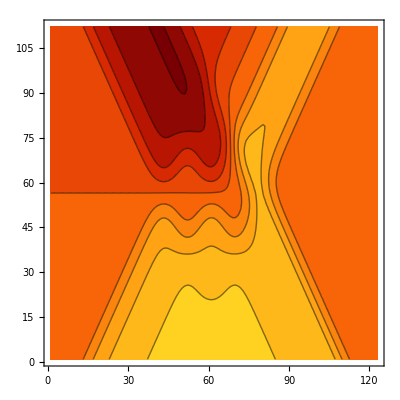

```mathematica
ListContourPlot[Table[IL*10^10,{V,-0.005,0.005,0.00009},{Vg,-0.003,0.008,0.00009}],ColorFunction->"Warm",PlotRange->All]
```

```mathematica
ListPlot3D[Table[Il[15]*10^10,{V,-0.005,0.005,0.00009},{Vg,-0.003,0.03,0.00009}],ColorFunction->"Warm",PlotRange->All]
```

-Graphics3D-

General::ivar: -0.005 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics3D-

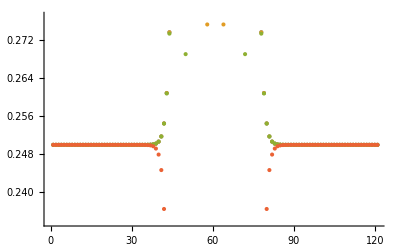

```mathematica
ListPlot3D[Table[Con[15]*10^10,{V,-0.005,0.005,0.00009},{Vg,-0.003,0.03,0.00009}],ColorFunction->"Warm",PlotRange->All]
PN=P/.Vg->0.0001;
ListPlot[Table[Table[PN[[i]],{V,-0.03,0.03,0.0005}],{i,1,4}]]
```

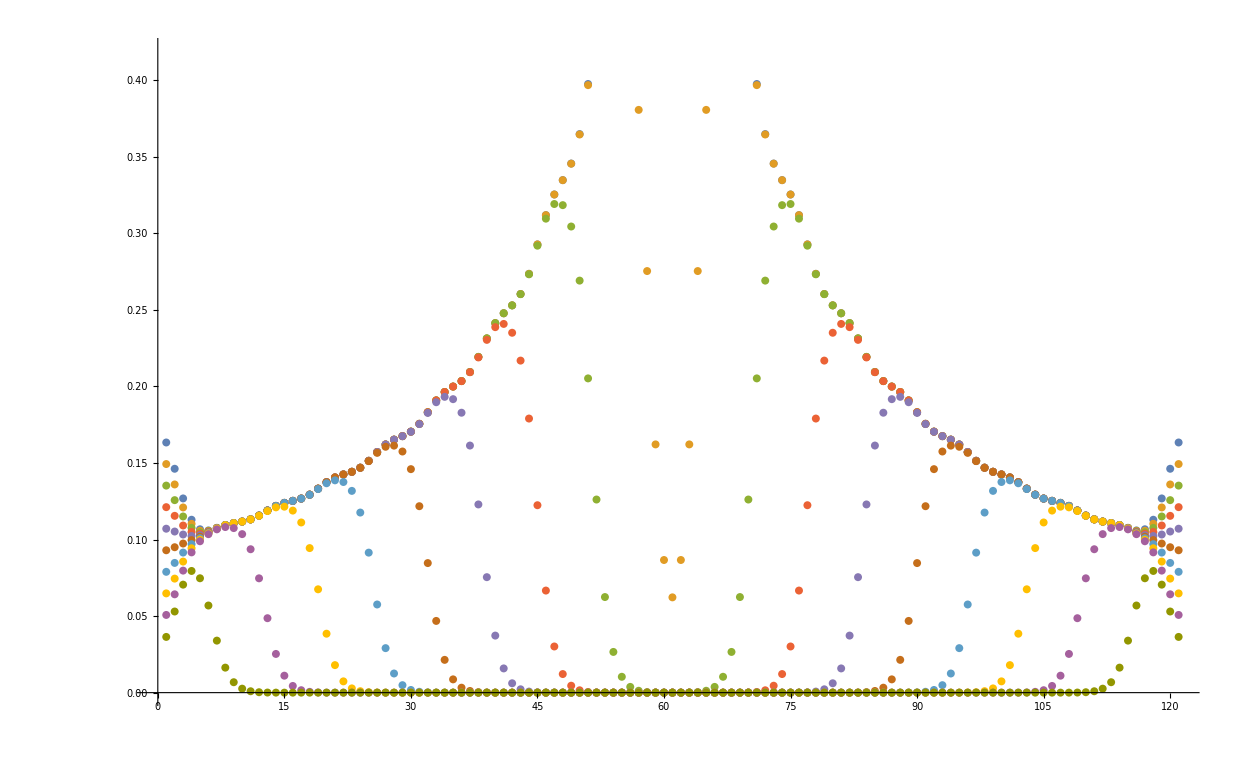

```mathematica
Pn1=Pn[10]/.Vg->0.0001;
ListPlot[Table[Table[Pn1[[i]],{V,-0.03,0.03,0.0005}],{i,1,10}]]
```

```mathematica
WMAT//MatrixForm
```

(1 | 1 | 1 | 1
1.30863 | -1.77777 | 0.913604 | 0
0 | 1.0864 | -1.76882 | 1.14478
0 | 0 | 0.855221 | -1.14478)

```mathematica
V=0.00002
Vg=0.0003
Wn[4]//MatrixForm
WMAT//MatrixForm
Pn[4]
WMAT+ConstantArray[1,{4,4}]
```

0.00002

0.0003

(1 | 1 | 1 | 1
0.251715 | -1.74887 | 1.99942 | 0
0 | 0.000584886 | -1.99942 | 2.
0 | 0 | 1.18847×10^-6 | -2.)

(1 | 1 | 1 | 1
0.251715 | -1.74887 | 1.99942 | 0
0 | 0.000584886 | -1.99942 | 2.
0 | 0 | 1.18847×10^-6 | -2.)

{0.87411,0.125853,0.0000368156,2.18771×10^-11}

{{2,2,2,2},{1.25172,-0.74887,2.99942,1},{1,1.00058,-0.999416,3.},{1,1,1.,-0.999999}}

```mathematica
TableForm[%164]
```

1. | 1. | 1. | 1.
1/(1.+2.71828^(1.81159×10^22 (1.2832×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (1.2832×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | -2.+1/(1.+2.71828^(1.81159×10^22 (1.2832×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (1.2832×10^-23+8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-3.84961×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-3.84961×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | 2.-1./(1.+2.71828^(1.81159×10^22 (3.84961×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (3.84961×10^-23+8.01×10^-20 V-1.602×10^-19 Vg))) | 0.
0. | 1/(1.+2.71828^(1.81159×10^22 (-1.2832×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (-1.2832×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | -2.+1/(1.+2.71828^(1.81159×10^22 (3.84961×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (3.84961×10^-23+8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-6.41601×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-6.41601×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | 2.-1./(1.+2.71828^(1.81159×10^22 (6.41601×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (6.41601×10^-23+8.01×10^-20 V-1.602×10^-19 Vg)))
0. | 0. | 1/(1.+2.71828^(1.81159×10^22 (-3.84961×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (-3.84961×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | -2.+1/(1.+2.71828^(1.81159×10^22 (6.41601×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (6.41601×10^-23+8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-8.98241×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-8.98241×10^-23+8.01×10^-20 V+1.602×10^-19 Vg)))

```mathematica
TableForm[%122]
```

1. | 1. | 1. | 1.
1/(1.+2.71828^(1.81159×10^22 (1.2832×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (1.2832×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | -2.+1/(1.+2.71828^(1.81159×10^22 (1.2832×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (1.2832×10^-23+8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-3.84961×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-3.84961×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | 2.-1./(1.+2.71828^(1.81159×10^22 (3.84961×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (3.84961×10^-23+8.01×10^-20 V-1.602×10^-19 Vg))) | 0.
0. | 1/(1.+2.71828^(1.81159×10^22 (-1.2832×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (-1.2832×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | -2.+1/(1.+2.71828^(1.81159×10^22 (3.84961×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (3.84961×10^-23+8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-6.41601×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-6.41601×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | 2.-1./(1.+2.71828^(1.81159×10^22 (6.41601×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (6.41601×10^-23+8.01×10^-20 V-1.602×10^-19 Vg)))
0. | 0. | 1/(1.+2.71828^(1.81159×10^22 (-3.84961×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (-3.84961×10^-23+8.01×10^-20 V+1.602×10^-19 Vg))) | -2.+1/(1.+2.71828^(1.81159×10^22 (6.41601×10^-23-8.01×10^-20 V-1.602×10^-19 Vg)))+1/(1.+2.71828^(1.81159×10^22 (6.41601×10^-23+8.01×10^-20 V-1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-8.98241×10^-23-8.01×10^-20 V+1.602×10^-19 Vg)))-1./(1.+2.71828^(1.81159×10^22 (-8.98241×10^-23+8.01×10^-20 V+1.602×10^-19 Vg)))

```mathematica
Dimensions[W]
```

{4,4}

```mathematica
Dimensions[%1239]
```

{4,4}

```mathematica
P
```

p

```mathematica
1.2832015033800003*^-13
```

1.2832×10^-13

```mathematica
EC
```

1.2832×10^-23

```mathematica
EN[1]
```

1.2832×10^-23-1.602×10^-19 Vg

```mathematica
EC
```

1.2832×10^-23

```mathematica
Band[{2,3},{4-1,4},{1,1}]
```

Band[{2,3},{3,4},{1,1}]

```mathematica
SparseArray[{Table[{1,i},{i,1,5}]->Table[1,5]},{5,5}]//MatrixForm
```

(1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Il[4]
```

```mathematica
ConstantArray[1,{4,4}]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

```mathematica
Table[1,3]
```

{1,1,1}

```mathematica
kb*T/EC
```

0.537717